### Start choosing the example:

```mathematica
t=30;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15];//Timing
```

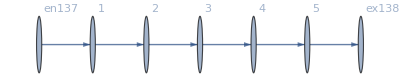

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→140.,u167→-15+140.,u168→-15+125.,u169→-15+110.,u170→-15+95.,u171→80,u172→140.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==13.0343&&15.-u162+1. u163==13.0343&&15.-u163+1. u164==13.0343&&95.-u164==13.0343

FRX1: The Error on the nonlinear terms is 2.19723×10^-14

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==13.0343&&15.-u162+1. u163==13.0343&&15.-u163+1. u164==13.0343&&95.-u164==13.0343

FRX1: The Error on the nonlinear terms is 2.19723×10^-14

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→87.8627,u162→85.897,u163→83.9313,u164→81.9657,u165→80,u166→0.+1. 87.8627,u167→0.+1. 85.897,u168→0.+1. 83.9313,u169→0.+1. 81.9657,u170→80.,u171→80,u172→0.+1. 87.8627|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==12.7677&&15.-u162+1. u163==12.7677&&15.-u163+1. u164==12.7677&&95.-u164==12.7677

FRX1: The Error on the nonlinear terms is 2.10369×10^-14

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==12.7677&&15.-u162+1. u163==12.7677&&15.-u163+1. u164==12.7677&&95.-u164==12.7677

FRX1: The Error on the nonlinear terms is 2.10369×10^-14

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→88.9294,u162→86.697,u163→84.4647,u164→82.2323,u165→80,u166→0.+1. 88.9294,u167→0.+1. 86.697,u168→0.+1. 84.4647,u169→0.+1. 82.2323,u170→80.,u171→80,u172→0.+1. 88.9294|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==12.0256&&15.-u162+1. u163==12.0256&&15.-u163+1. u164==12.0256&&95.-u164==12.0256

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==12.0256&&15.-u162+1. u163==12.0256&&15.-u163+1. u164==12.0256&&95.-u164==12.0256

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→91.8975,u162→88.9232,u163→85.9488,u164→82.9744,u165→80,u166→0.+1. 91.8975,u167→0.+1. 88.9232,u168→0.+1. 85.9488,u169→0.+1. 82.9744,u170→80.,u171→80,u172→0.+1. 91.8975|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==4.16261&&15.-u162+1. u163==4.16261&&15.-u163+1. u164==4.16261&&95.-u164==4.16261

FRX1: The Error on the nonlinear terms is 3.75984×10^-14

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==4.16261&&15.-u162+1. u163==4.16261&&15.-u163+1. u164==4.16261&&95.-u164==4.16261

FRX1: The Error on the nonlinear terms is 3.75984×10^-14

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→123.35,u162→112.512,u163→101.675,u164→90.8374,u165→80,u166→0.+1. 123.35,u167→0.+1. 112.512,u168→0.+1. 101.675,u169→0.+1. 90.8374,u170→80.,u171→80,u172→0.+1. 123.35|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==0&&15.-u162+1. u163==0&&15.-u163+1. u164==0&&95.-u164==0

FRX1: The Error on the nonlinear terms is 3.19744×10^-14

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→0.+1. 140.,u167→0.+1. 125.,u168→0.+1. 110.,u169→0.+1. 95.,u170→80.,u171→80,u172→0.+1. 140.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-19.4284&&15.-u162+1. u163==-19.4284&&15.-u163+1. u164==-19.4284&&95.-u164==-19.4284

FRX1: The Error on the nonlinear terms is 4.26326×10^-14

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-19.4284&&15.-u162+1. u163==-19.4284&&15.-u163+1. u164==-19.4284&&95.-u164==-19.4284

FRX1: The Error on the nonlinear terms is 4.26326×10^-14

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→217.714,u162→183.285,u163→148.857,u164→114.428,u165→80,u166→0.+1. 217.714,u167→0.+1. 183.285,u168→0.+1. 148.857,u169→0.+1. 114.428,u170→80.,u171→80,u172→0.+1. 217.714|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-274.847&&15.-u162+1. u163==-274.847&&15.-u163+1. u164==-274.847&&95.-u164==-274.847

FRX1: The Error on the nonlinear terms is 1.13687×10^-13

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-274.847&&15.-u162+1. u163==-274.847&&15.-u163+1. u164==-274.847&&95.-u164==-274.847

FRX1: The Error on the nonlinear terms is 1.13687×10^-13

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→1239.39,u162→949.54,u163→659.693,u164→369.847,u165→80,u166→0.+1. 1239.39,u167→0.+1. 949.54,u168→0.+1. 659.693,u169→0.+1. 369.847,u170→80.,u171→80,u172→0.+1. 1239.39|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-976.&&15.-u162+1. u163==-976.&&15.-u163+1. u164==-976.&&95.-u164==-976.

FRX1: The Error on the nonlinear terms is 0.

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-976.&&15.-u162+1. u163==-976.&&15.-u163+1. u164==-976.&&95.-u164==-976.

FRX1: The Error on the nonlinear terms is 0.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→4044.,u162→3053.,u163→2062.,u164→1071.,u165→80,u166→0.+1. 4044.,u167→0.+1. 3053.,u168→0.+1. 2062.,u169→0.+1. 1071.,u170→80.,u171→80,u172→0.+1. 4044.|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-977.455&&15.-u162+1. u163==-977.455&&15.-u163+1. u164==-977.455&&95.-u164==-977.455

FRX1: The Error on the nonlinear terms is 6.82121×10^-13

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-977.455&&15.-u162+1. u163==-977.455&&15.-u163+1. u164==-977.455&&95.-u164==-977.455

FRX1: The Error on the nonlinear terms is 6.82121×10^-13

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→4049.82,u162→3057.36,u163→2064.91,u164→1072.45,u165→80,u166→0.+1. 4049.82,u167→0.+1. 3057.36,u168→0.+1. 2064.91,u169→0.+1. 1072.45,u170→80.,u171→80,u172→0.+1. 4049.82|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1052.2&&15.-u162+1. u163==-1052.2&&15.-u163+1. u164==-1052.2&&95.-u164==-1052.2

FRX1: The Error on the nonlinear terms is 0.

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1052.2&&15.-u162+1. u163==-1052.2&&15.-u163+1. u164==-1052.2&&95.-u164==-1052.2

FRX1: The Error on the nonlinear terms is 0.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→4348.79,u162→3281.6,u163→2214.4,u164→1147.2,u165→80,u166→0.+1. 4348.79,u167→0.+1. 3281.6,u168→0.+1. 2214.4,u169→0.+1. 1147.2,u170→80.,u171→80,u172→0.+1. 4348.79|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1135.97&&15.-u162+1. u163==-1135.97&&15.-u163+1. u164==-1135.97&&95.-u164==-1135.97

FRX1: The Error on the nonlinear terms is 4.54747×10^-13

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1135.97&&15.-u162+1. u163==-1135.97&&15.-u163+1. u164==-1135.97&&95.-u164==-1135.97

FRX1: The Error on the nonlinear terms is 4.54747×10^-13

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→4683.87,u162→3532.9,u163→2381.94,u164→1230.97,u165→80,u166→0.+1. 4683.87,u167→0.+1. 3532.9,u168→0.+1. 2381.94,u169→0.+1. 1230.97,u170→80.,u171→80,u172→0.+1. 4683.87|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1330.01&&15.-u162+1. u163==-1330.01&&15.-u163+1. u164==-1330.01&&95.-u164==-1330.01

FRX1: The Error on the nonlinear terms is 4.54747×10^-13

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1330.01&&15.-u162+1. u163==-1330.01&&15.-u163+1. u164==-1330.01&&95.-u164==-1330.01

FRX1: The Error on the nonlinear terms is 4.54747×10^-13

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→5460.02,u162→4115.02,u163→2770.01,u164→1425.01,u165→80,u166→0.+1. 5460.02,u167→0.+1. 4115.02,u168→0.+1. 2770.01,u169→0.+1. 1425.01,u170→80.,u171→80,u172→0.+1. 5460.02|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2222.01&&15.-u162+1. u163==-2222.01&&15.-u163+1. u164==-2222.01&&95.-u164==-2222.01

FRX1: The Error on the nonlinear terms is 9.09495×10^-13

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2222.01&&15.-u162+1. u163==-2222.01&&15.-u163+1. u164==-2222.01&&95.-u164==-2222.01

FRX1: The Error on the nonlinear terms is 9.09495×10^-13

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→9028.05,u162→6791.04,u163→4554.03,u164→2317.01,u165→80,u166→0.+1. 9028.05,u167→0.+1. 6791.04,u168→0.+1. 4554.03,u169→0.+1. 2317.01,u170→80.,u171→80,u172→0.+1. 9028.05|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-6189.42&&15.-u162+1. u163==-6189.42&&15.-u163+1. u164==-6189.42&&95.-u164==-6189.42

FRX1: The Error on the nonlinear terms is 3.63798×10^-12

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-6189.42&&15.-u162+1. u163==-6189.42&&15.-u163+1. u164==-6189.42&&95.-u164==-6189.42

FRX1: The Error on the nonlinear terms is 3.63798×10^-12

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→24897.7,u162→18693.2,u163→12488.8,u164→6284.42,u165→80,u166→0.+1. 24897.7,u167→0.+1. 18693.2,u168→0.+1. 12488.8,u169→0.+1. 6284.42,u170→80.,u171→80,u172→0.+1. 24897.7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-144134.&&15.-u162+1. u163==-144134.&&15.-u163+1. u164==-144134.&&95.-u164==-144134.

FRX1: The Error on the nonlinear terms is 0.

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-144134.&&15.-u162+1. u163==-144134.&&15.-u163+1. u164==-144134.&&95.-u164==-144134.

FRX1: The Error on the nonlinear terms is 0.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→576674.,u162→432526.,u163→288377.,u164→144229.,u165→80,u166→0.+1. 576674.,u167→0.+1. 432526.,u168→0.+1. 288377.,u169→0.+1. 144229.,u170→80.,u171→80,u172→0.+1. 576674.|>

```mathematica
alpha = 1.89;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-6.39369×10^7&&15.-u162+1. u163==-6.39369×10^7&&15.-u163+1. u164==-6.39369×10^7&&95.-u164==-6.39369×10^7

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→140.,u167→-15+140.,u168→-15+125.,u169→-15+110.,u170→-15+95.,u171→80,u172→140.|>

```mathematica
alpha = 1.9;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2.0309×10^8&&15.-u162+1. u163==-2.0309×10^8&&15.-u163+1. u164==-2.0309×10^8&&95.-u164==-2.0309×10^8

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→140.,u167→-15+140.,u168→-15+125.,u169→-15+110.,u170→-15+95.,u171→80,u172→140.|>

```mathematica
alpha = 1.95;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-5.02628×10^12&&15.-u162+1. u163==-5.02628×10^12&&15.-u163+1. u164==-5.02628×10^12&&95.-u164==-5.02628×10^12

FRX1: The Error on the nonlinear terms is 0.

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-5.02628×10^12&&15.-u162+1. u163==-5.02628×10^12&&15.-u163+1. u164==-5.02628×10^12&&95.-u164==-5.02628×10^12

FRX1: The Error on the nonlinear terms is 0.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→2.01051×10^13,u162→1.50788×10^13,u163→1.00526×10^13,u164→5.02628×10^12,u165→80,u166→0.+1. 2.01051×10^13,u167→0.+1. 1.50788×10^13,u168→0.+1. 1.00526×10^13,u169→0.+1. 5.02628×10^12,u170→80.,u171→80,u172→0.+1. 2.01051×10^13|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2.91158×10^27&&15.-u162+1. u163==-2.91158×10^27&&15.-u163+1. u164==-2.91158×10^27&&95.-u164==-2.91158×10^27

FRX1: The Error on the nonlinear terms is 0.

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2.91158×10^27&&15.-u162+1. u163==-2.91158×10^27&&15.-u163+1. u164==-2.91158×10^27&&95.-u164==-2.91158×10^27

FRX1: The Error on the nonlinear terms is 0.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→1.16463×10^28,u162→8.73473×10^27,u163→5.82316×10^27,u164→2.91158×10^27,u165→80,u166→0.+1. 1.16463×10^28,u167→0.+1. 8.73473×10^27,u168→0.+1. 5.82316×10^27,u169→0.+1. 2.91158×10^27,u170→80.,u171→80,u172→0.+1. 1.16463×10^28|>

```mathematica
alpha = 1.999;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-2.03684×10^45&&15.-u162+1. u163==-2.03684×10^45&&15.-u163+1. u164==-2.03684×10^45&&95.-u164==-2.03684×10^45

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→140.,u167→-15+140.,u168→-15+125.,u169→-15+110.,u170→-15+95.,u171→80,u172→140.|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j145==jt151&&j144==jt152&&j139==jt153&&j146==jt154&&j140==jt155&&j147==jt156&&j141==jt157&&j148==jt158&&j142==jt159&&j149==jt160&&j139==jt152&&j150==jt151&&j145==jt154&&j140==jt153&&j146==jt156&&j141==jt155&&j147==jt158&&j142==jt157&&j148==jt160&&j143==jt159&&j144==15&&u171==80&&-u166+u172==0&&-u165+u171==0&&jt151==0&&jt160==0

EEX: -u161+u166==0.&&-u162+u167==0.&&-u163+u168==0.&&-u164+u169==0.&&-80+u170==0.

EEX: 15.-u161+1. u162==-1.19877×10^50&&15.-u162+1. u163==-1.19877×10^50&&15.-u163+1. u164==-1.19877×10^50&&95.-u164==-1.19877×10^50

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j139→15,j140→15,j141→15,j142→15,j143→15,j144→15,j145→0,j146→0,j147→0,j148→0,j149→0,j150→0,jt151→0,jt152→15,jt153→15,jt154→0,jt155→15,jt156→0,jt157→15,jt158→0,jt159→15,jt160→0,u161→140.,u162→125.,u163→110.,u164→95.,u165→80,u166→140.,u167→-15+140.,u168→-15+125.,u169→-15+110.,u170→-15+95.,u171→80,u172→140.|>

### What we this plot for?

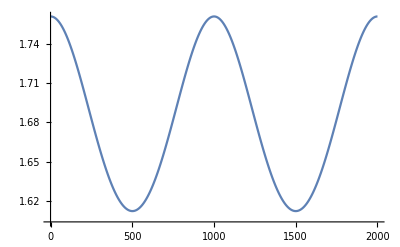

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.